# Vector Spherical Harmonics

Fourier Integrals of Vector spherical harmonics obey identities that are crucial to relating near and far fields. In a numerical calculation, the accuracy to which these identities are obeyed determines the accuracy of a near to far field transformation that relies on near field data. It has been frustrating to test the implementation in this respect while being unsure whether “small deviations” were implementation or rounding errors. In order to get out of this confusion, I have implemented here the test for evaluating both the left and the right hand side of the integral identities below. The left hand side is an integral over the surface of the sphere and is computed in the two dimensional plane (θ, ϕ). The right hand side is evaluated directly from the special functions inside Mathematica.

The notebook creates a table of vector spherical harmonics up to L = 3. This table is cross-checked with that published:


The table is then cross-checked against my python implementation.

## Definitions

### Coordinate System

```mathematica
r̂[θ_,ϕ_]:={Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
θ̂[θ_,ϕ_]:={ Cos[θ]Cos[ϕ], Cos[θ]Sin[ϕ], -Sin[θ]}
ϕ̂[θ_,ϕ_]:={-Sin[ϕ], Cos[ϕ], 0};
cart[{u_,θ_,ϕ_}]:=u {Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]};
```

Check that the cross product triad is obeyed

r̂×θ̂ = ϕ̂

```mathematica
FullSimplify[Cross[r̂[θ,ϕ],θ̂[θ,ϕ]]] == ϕ̂[θ,ϕ]
```

True

### Spherical Bessel functions and Vector Harmonics

```mathematica
ψ[l_,z_] := z SphericalBesselJ[l,z]
Dψ[l_,z_]:= Evaluate[D[ψ[l,z],z]]
LY[l_,m_,θ_,ϕ_]:=1/(√(l (l+1))){
1/2(√((l-m) (l+m+1)) SphericalHarmonicY[l,m+1,θ,ϕ]+√((l+m) (l-m+1)) SphericalHarmonicY[l,m-1,θ,ϕ]),
1/(2ⅈ)(√((l-m) (l+m+1)) SphericalHarmonicY[l,m+1,θ,ϕ]-√((l+m) (l-m+1)) SphericalHarmonicY[l,m-1,θ,ϕ]),
m SphericalHarmonicY[l,m,θ,ϕ]
}

A1[l_,m_,θ_,ϕ_]:=-ⅈ LY[l,m,θ,ϕ]
A2[l_,m_,θ_,ϕ_]:=Cross[rhat[θ,ϕ],A1[l,m,θ,ϕ]]
A3[l_,m_,θ_,ϕ_]:=SphericalHarmonicY[l,m,θ,ϕ] r̂[θ,ϕ]

M1[l_,m_,z_,θ_,ϕ_]:= SphericalBesselJ[l,z] A1[l,m,θ,ϕ]
N1[l_,m_,z_,θ_,ϕ_]:= Dψ[l,z]/z A2[l,m,θ,ϕ]+√(l(l+1)) SphericalBesselJ[l,z]/z A3[l,m,θ,ϕ]
```

### Integral Identities

From my notes, the following identities can be proven by using the plane wave expansion into spherical harmonics. I will evaluate the left hand side with NIntegrate.

```mathematica
lhs1[L_,M_,ksph_]:=NIntegrate[ Exp[-ⅈ cart[ksph].rhat[θ,ϕ]] A1[L,M, θ,ϕ] Sin[θ],{θ,0,π},{ϕ,0,2 π},AccuracyGoal-> 5];
lhs2[L_,M_,ksph_]:=NIntegrate[ Exp[-ⅈ cart[ksph].rhat[θ,ϕ]] A2[L,M, θ,ϕ] Sin[θ],{θ,0,π},{ϕ,0,2 π},AccuracyGoal-> 5];

rhs1[L_,M_,ksph_]:=4 π ⅈ^-L M1[L,M,ksph[[1]],ksph[[2]],ksph[[3]]];
rhs2[L_,M_,ksph_]:=4 π ⅈ^(-L+1) N1[L,M,ksph[[1]],ksph[[2]],ksph[[3]]];
```

## Tables

### Table of Vector Spherical Harmonics

Mignard and Kiloner define their coordinate system (u, α, δ), such that it corresponds to my definitions via

α=ϕ
δ=π/2-θ
e_α= ϕ̂
e_δ= -θ̂

I will produce the table in their notation so that it can be compared directly with their table A.1 The transformation is, for a vector F (θ,ϕ) = (F_θ(θ,ϕ),F_ϕ(θ,ϕ)) ,

F_lm  ← (0 | 1
-1 | 0)  (-1)^m F_lm(π/2-δ, α)

Their Vector spherical harmonics correspond to mine via

T_lm  = (-1)^m A_(1lm)
S_lm  = (-1)^m A_(2lm)

```mathematica
t[L_,m_]:=FullSimplify[{A1[L,m,θ,α].ϕ̂[θ,α],-A1[L,m,θ,α].θ̂[θ,α]}/.θ-> π/2-δ]
s[L_,m_]:=FullSimplify[{A2[L,m,θ,α].ϕ̂[θ,α],-A2[L,m,θ,α].θ̂[θ,α]}/.θ-> π/2-δ]
```

```mathematica
ttable = Flatten[Table[Table[ t[l,m],{m,0,l}],{l,1,2}],1];
TraditionalForm[ttable]
```

(1/2 √(3/(2 π)) cos(δ) | 0
1/4 √(3/π) ⅇ^(ⅈ α) sin(δ) | 1/4 ⅈ √(3/π) ⅇ^(ⅈ α)
1/2 √(15/(2 π)) sin(δ) cos(δ) | 0
-1/4 √(5/π) ⅇ^(ⅈ α) cos(2 δ) | 1/4 ⅈ √(5/π) ⅇ^(ⅈ α) sin(δ)
-1/4 √(5/π) ⅇ^(2 ⅈ α) sin(δ) cos(δ) | -1/4 ⅈ √(5/π) ⅇ^(2 ⅈ α) cos(δ))

```mathematica
stable = Flatten[Table[Table[ s[l,m],{m,0,l}],{l,1,2}],1];
TraditionalForm[stable]
```

(0 | 1/2 √(3/(2 π)) cos(δ)
1/4 √(3/π) (sin(α)-ⅈ cos(α)) | 1/4 √(3/π) ⅇ^(ⅈ α) sin(δ)
0 | 1/2 √(15/(2 π)) sin(δ) cos(δ)
1/4 √(5/π) sin(δ) (sin(α)-ⅈ cos(α)) | -1/4 √(5/π) ⅇ^(ⅈ α) cos(2 δ)
1/4 ⅈ √(5/π) ⅇ^(2 ⅈ α) cos(δ) | -1/4 √(5/π) ⅇ^(2 ⅈ α) sin(δ) cos(δ))

### Integral Identities

```mathematica
ksph={1.,π/3,0};
cart[ksph]
ITable1 = Table[Table[  Join[{l,m},Chop[lhs1[l,m,ksph]], rhs1[l,m,ksph]],{m,0,l}],{l,1,3}];
ITable2 = Table[Table[  Join[{l,m},Chop[lhs2[l,m,ksph]], rhs2[l,m,ksph]],{m,0,l}],{l,1,3}];
```

{0.866025,0.,0.5}

```mathematica
TraditionalForm[Grid[Flatten[ITable1,1],Frame-> All]]
TraditionalForm[Grid[Flatten[ITable2,1],Frame-> All]]
```

1 | 0 | 0 | 0.-1.13238 ⅈ | 0 | 0.+0. ⅈ | 0.-1.13238 ⅈ | 0.+0. ⅈ
1 | 1 | -0.462291-3.69126×10^-10 ⅈ | 3.69126×10^-10-0.462291 ⅈ | 0.800711 | -0.462291+0. ⅈ | 0.-0.462291 ⅈ | 0.800711+0. ⅈ
2 | 0 | 0 | -0.260779+1.11356×10^-10 ⅈ | 0 | 0. | -0.260779 | 0.
2 | 1 | 1.05082×10^-9+0.0614663 ⅈ | 0.122933 | 0.-0.106463 ⅈ | 0.+0.0614663 ⅈ | 0.122933 | 0.-0.106463 ⅈ
2 | 2 | 0.-0.106463 ⅈ | 0.106463 | 4.66594×10^-10+0.184399 ⅈ | 0.-0.106463 ⅈ | 0.106463 | 0.+0.184399 ⅈ
3 | 0 | 0 | 0.+0.00791929 ⅈ | 0 | 0.+0. ⅈ | 0.+0.00791927 ⅈ | 0.+0. ⅈ
3 | 1 | 0.00131987-3.08914×10^-10 ⅈ | 0.-0.0382765 ⅈ | -0.00228609 | 0.00131988+0. ⅈ | 0.-0.0382765 ⅈ | -0.0022861+0. ⅈ
3 | 2 | -0.0144585 | 0.+0.00722926 ⅈ | 0.0250442 | -0.0144585+0. ⅈ | 0.+0.00722927 ⅈ | 0.0250429+0. ⅈ
3 | 3 | 0.0153356 | 1.02442×10^-10+0.0153356 ⅈ | -0.026562 | 0.0153356+0. ⅈ | 0.+0.0153356 ⅈ | -0.026562+0. ⅈ

1 | 0 | 0.116624 | 0 | 2.41311 | 0.116624 | 0. | 2.41311
1 | 1 | -1.80155 | 0.-1.65872 ⅈ | -0.0824657-1.27348×10^-10 ⅈ | -1.80155 | 0.-1.65872 ⅈ | -0.0824657
2 | 0 | 0.+0.502628 ⅈ | 0 | 0.-0.569455 ⅈ | 0.+0.502628 ⅈ | 0.+0. ⅈ | 0.-0.569455 ⅈ
2 | 1 | 0.+0.377722 ⅈ | -0.35095 | -5.64305×10^-10+0.62332 ⅈ | 0.+0.377722 ⅈ | -0.35095+0. ⅈ | 0.+0.62332 ⅈ
2 | 2 | -2.99005×10^-9-0.631048 ⅈ | 0.607863 | 7.04125×10^-10-0.013386 ⅈ | 0.-0.631048 ⅈ | 0.607863+0. ⅈ | 0.-0.013386 ⅈ
3 | 0 | 0.126264 | 0 | 0.0373475 | 0.126264 | 0. | 0.0373474
3 | 1 | -0.0506468 | 0.+0.0102627 ⅈ | 0.142589 | -0.0506468 | 0.+0.0102627 ⅈ | 0.142589
3 | 2 | -0.116074+3.92694×10^-9 ⅈ | -4.1043×10^-9-0.112422 ⅈ | -0.0994689+6.0295×10^-10 ⅈ | -0.116074 | 0.-0.112422 ⅈ | -0.0994689
3 | 3 | 0.121824 | -4.61242×10^-9+0.119242 ⅈ | 0.00149083-1.88929×10^-9 ⅈ | 0.121824 | 0.+0.119242 ⅈ | 0.00149083

```mathematica
r̂[π/4.,0.]
```

{0.707107,0.,0.707107}

### Values of A_1, A_2

```mathematica
th = π/3.
ph = 0.
TraditionalForm[Grid[Flatten[Table[Table[  Join[{l,m},A1[l,m,th,ph]],{m,0,l}],{l,1,3}],1],Frame-> All]]
TraditionalForm[Grid[Flatten[Table[Table[  Join[{l,m},A2[l,m,th,ph]],{m,0,l}],{l,1,3}],1],Frame-> All]]
TraditionalForm[Grid[Flatten[Table[Table[  Join[{l,m},A3[l,m,th,ph]],{m,0,l}],{l,1,3}],1],Frame-> All]]
```

1.0472

0.

1 | 0 | 0.+0. ⅈ | 0.299207+0. ⅈ | 0.+0. ⅈ
1 | 1 | 0.-0.122151 ⅈ | 0.122151+0. ⅈ | 0.+0.211571 ⅈ
2 | 0 | 0.+0. ⅈ | 0.334523+0. ⅈ | 0.+0. ⅈ
2 | 1 | 0.-0.0788479 ⅈ | -0.157696+0. ⅈ | 0.+0.136569 ⅈ
2 | 2 | 0.+0.136569 ⅈ | -0.136569+0. ⅈ | 0.-0.236544 ⅈ
3 | 0 | 0.+0. ⅈ | 0.0699706+0. ⅈ | 0.+0. ⅈ
3 | 1 | 0.-0.0116618 ⅈ | -0.338191+0. ⅈ | 0.+0.0201988 ⅈ
3 | 2 | 0.+0.127748 ⅈ | 0.0638741+0. ⅈ | 0.-0.221266 ⅈ
3 | 3 | 0.-0.135497 ⅈ | 0.135497+0. ⅈ | 0.+0.234688 ⅈ

1 | 0 | -0.149603+0. ⅈ | 0. | 0.259121+0. ⅈ
1 | 1 | -0.0610753+0. ⅈ | 0.-0.244301 ⅈ | 0.105786+0. ⅈ
2 | 0 | -0.167262+0. ⅈ | 0. | 0.289706+0. ⅈ
2 | 1 | 0.0788479+0. ⅈ | 0.-0.157696 ⅈ | -0.136569+0. ⅈ
2 | 2 | 0.0682843+0. ⅈ | 0.+0.273137 ⅈ | -0.118272+0. ⅈ
3 | 0 | -0.0349853+0. ⅈ | 0. | 0.0605963+0. ⅈ
3 | 1 | 0.169096+0. ⅈ | 0.-0.0233235 ⅈ | -0.292882+0. ⅈ
3 | 2 | -0.031937+0. ⅈ | 0.+0.255496 ⅈ | 0.0553166+0. ⅈ
3 | 3 | -0.0677487+0. ⅈ | 0.-0.270995 ⅈ | 0.117344+0. ⅈ

1 | 0 | 0.211571 | 0. | 0.122151
1 | 1 | -0.259121 | 0. | -0.149603
2 | 0 | -0.0682843 | 0. | -0.0394239
2 | 1 | -0.289706 | 0. | -0.167262
2 | 2 | 0.250892 | 0. | 0.144853
3 | 0 | -0.282783 | 0. | -0.163265
3 | 1 | -0.0605963 | 0. | -0.0349853
3 | 2 | 0.3319 | 0. | 0.191622
3 | 3 | -0.234688 | 0. | -0.135497

```mathematica
th = π/3.;
ph = 0.;
TraditionalForm[Grid[Flatten[Table[Table[  Join[{l,m},M1[l,m,2,th,ph]],{m,0,l}],{l,1,3}],1],Frame-> All]]
TraditionalForm[Grid[Flatten[Table[Table[  Join[{l,m},N1[l,m,2,th,ph]],{m,0,l}],{l,1,3}],1],Frame-> All]]
```

1 | 0 | 0.+0. ⅈ | 0.130274+0. ⅈ | 0.+0. ⅈ
1 | 1 | 0.-0.0531841 ⅈ | 0.0531841+0. ⅈ | 0.+0.0921176 ⅈ
2 | 0 | 0.+0. ⅈ | 0.0663855+0. ⅈ | 0.+0. ⅈ
2 | 1 | 0.-0.0156472 ⅈ | -0.0312944+0. ⅈ | 0.+0.0271017 ⅈ
2 | 2 | 0.+0.0271017 ⅈ | -0.0271017+0. ⅈ | 0.-0.0469416 ⅈ
3 | 0 | 0.+0. ⅈ | 0.00424876+0. ⅈ | 0.+0. ⅈ
3 | 1 | 0.-0.000708127 ⅈ | -0.0205357+0. ⅈ | 0.+0.00122651 ⅈ
3 | 2 | 0.+0.00775714 ⅈ | 0.00387857+0. ⅈ | 0.-0.0134358 ⅈ
3 | 3 | 0.-0.00822769 ⅈ | 0.00822769+0. ⅈ | 0.+0.0142508 ⅈ

1 | 0 | 0.0296885+0. ⅈ | 0. | 0.0990054+0. ⅈ
1 | 1 | -0.094248+0. ⅈ | 0.-0.0578871 ⅈ | -0.0209929+0. ⅈ
2 | 0 | -0.056229+0. ⅈ | 0. | 0.0590638+0. ⅈ
2 | 1 | -0.0517294+0. ⅈ | 0.-0.037366 ⅈ | -0.0730125+0. ⅈ
2 | 2 | 0.0771589+0. ⅈ | 0.+0.0647198 ⅈ | 0.00718171+0. ⅈ
3 | 0 | -0.0334975+0. ⅈ | 0. | -0.0106652+0. ⅈ
3 | 1 | 0.0117818+0. ⅈ | 0.-0.00250413 ⅈ | -0.0351248+0. ⅈ
3 | 2 | 0.0314782+0. ⅈ | 0.+0.0274313 ⅈ | 0.0260927+0. ⅈ
3 | 3 | -0.0319569+0. ⅈ | 0.-0.0290953 ⅈ | -0.00165214+0. ⅈ

```mathematica
N[N1[1,0,1,π/3,0] 4π ]
```

{0.116624,0.,2.41311}

```mathematica
rhs2[1,0,1,π/3,0]
```

rhs2[1,0,1,π/3,0]

```mathematica
temp[1.,0,2,π/3.,0.]
```

{0.23695,0.307873,0.217699}

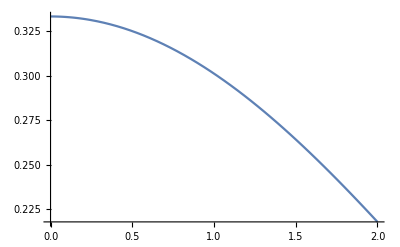

```mathematica
Plot[SphericalBesselJ[1,z]/z,{z,0,2}]
```

```mathematica
N[ψ[1,2]/4 Sqrt[6]]
```

0.533251